```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
l=45;
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,l}];
Tc=Table[Max[Table[If[1/fpiall[[j]][[i]]<1&&1/fpiall[[j]][[i+1]]>100,i,0],{i,1,Length[fpiall[[j]]]}]],{j,1,l}]
mub=Flatten[Table[i*13,{i,1,l}]]
```

{118,118,118,118,118,118,117,117,117,116,116,115,115,114,114,113,112,112,111,110,109,108,107,106,105,104,103,101,100,98,97,95,93,92,90,88,85,83,81,78,75,72,69,66,62}

{13,26,39,52,65,78,91,104,117,130,143,156,169,182,195,208,221,234,247,260,273,286,299,312,325,338,351,364,377,390,403,416,429,442,455,468,481,494,507,520,533,546,559,572,585}

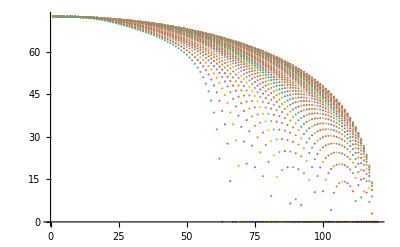

```mathematica
ListPlot[fpiall]
```

```mathematica
mub2=Flatten[{mub,600}];
Tc2=Flatten[{Tc,57.916430}];
```

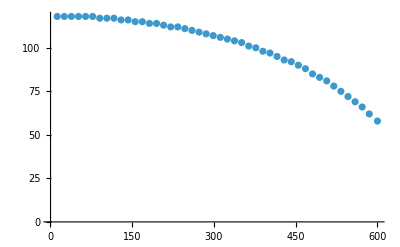

```mathematica
ListPlot[Transpose[{mub2,Tc2}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub2,Tc2}],a+b x^2+c x^4,{a,b,c},x]
```

{a→117.955,b→-0.000101378,c→-1.76668×10^-10}

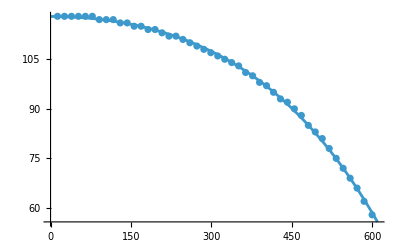

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,610}],ListPlot[Transpose[{mub2,Tc2}]]]
```

```mathematica
mub={0,100,200,300,400,500,550,575,600};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
Export["pb.dat",phaseboundary]
```

pb.dat

```mathematica
mub2=Table[i,{i,0,600,10}];
Tc2=Table[{mub2[[i]],a+b mub2[[i]]^2+c mub2[[i]]^4/.fitpd},{i,1,Length[mub2]}];
Export["pb2nd.dat",Tc2]
```

pb2nd.dat